# Density Plot

## Start

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Append[$Path,#]&/@FileNames["*",{Directory[]<>"\1DPackage"}];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalStereoAll`"
<<"PixelTest`"
<<"LineTest`"
```

## read

```mathematica
read[set_,num_,reduce_,corf_]:=Module[{ia,ib,id,rgb2d,reduire,clean,io,left,right,disp,occ, frame, base,fileleft,fileright},(

base="D:\MastersMathematica\Data\Sintel";

frame="frame_"<>num<>".png";
fileleft=corf<>"_left";
fileright=corf<>"_right";
left=FileNameJoin[{base,"training",fileleft,set,frame}];
right=FileNameJoin[{base,"training",fileright,set,frame}];
disp=FileNameJoin[{base,"training","disparities",set,frame}];
occ=FileNameJoin[{base,"training","occlusions",set,frame}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];
reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];
ia=reduire[ColorConvert[clean@Import[left],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[right],"GrayScale"],reduce];
id=reduire[Image[
rgb2d[Flatten[N@ImageData[clean@Import[disp],"Byte"],{{3},{1},{2}}]]
],reduce]/reduce;
io=reduire[ColorConvert[clean@Import[occ],"GrayScale"],reduce];
read[{left,right,disp,occ},reduce]={ia,ib,id,io};

{ia,ib,id,io}
)];
```

## Test Design

#### Pythagoras

```mathematica
pyth[{x_,y_}]:=Sqrt[(x^2+y^2)]
```

#### RMSE

```mathematica
rmse[x_,y_]:=N@Sqrt[Mean[Power[x-y,2]]]
```

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

#### count colors

```mathematica
(*Counts the amount of colors in solution*)
countColors[v_]:=Block[{count},
count=0;
ImageScan[If[Mean[#]≠0,count++]&,v];
count
]
```

#### N tests

```mathematica
(*Error is updated depending in the highest res level *)test1[ia_,ib_,lvlmax_,e_,mode_]:=Block[{},(

Table[
stereoDepth[ia,ib,lvlmax,{1,i},e,mode]
,{i,lvlmax}]

)]
```

#### results

```mathematica
res1Display[res1_,id_]:=Block[{maxid,flipMask, signMask, magMask, okMask, convergedMask,imageConverged, imageOk, imageFlip, imageSign, imageMag},(
maxid=MinMax[Flatten[ImageData[id]]][[2]];
npixels=103.*45.;

(*"converged", "ok","oksign","flip","sign","mag"*)
flipMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Orange,"sign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Red,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"oksign"->Blue,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};

Table[
imageConverged=Image[res[[All,All,2]]/.convergedMask];
imageOk=Image[res[[All,All,2]]/.okMask];
imageFlip=Image[res[[All,All,2]]/.flipMask];
imageSign=Image[res[[All,All,2]]/.signMask];
imageMag=Image[res[[All,All,2]]/.magMask];

lst1=Flatten[-res[[All,All,1]]];
lst2=Flatten[ImageData[id]];
p=Flatten[Position[Flatten[res[[All,All,2]]],#]&/@{"sign","mag","flip","ok","oksign"},1];
lst11=Delete[lst1,p];
lst22=Delete[lst2,p];

{Image[-res[[All,All,1]]]/(maxid),
id/(maxid),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}],
rmse[lst11,lst22],
rmse[lst1,lst2],
1./countColors[imageConverged]
}
,{res, res1}]
)]
```

#### Display of results

```mathematica
res2ColorCode[result_,id_]:=Block[{},(
minmaxid=MinMax[Flatten[ImageData[id]]];
(*seeStatus={"converged"->Transparent,"ok"->Transparent,"flip"->Red,"sign"->Purple,"mag"->Yellow};*)
flipMask={"converged"->Transparent,"ok"->Transparent,"flip"->Orange,"sign"->Transparent,"oksign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Red,"oksign"->Transparent,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"oksign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"flip"->Transparent,"sign"->Transparent,"oksign"->Blue,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"oksign"->Transparent,"mag"->Transparent};

imageConverged=Image[result[[All,All,2]]/.convergedMask];
imageOk=Image[result[[All,All,2]]/.okMask];
imageFlip=Image[result[[All,All,2]]/.flipMask];
imageSign=Image[result[[All,All,2]]/.signMask];
imageMag=Image[result[[All,All,2]]/.magMask];

{Image[-result[[All,All,1]]]/(minmaxid[[2]]),
id/(minmaxid[[2]]),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}]}

)]
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read["bamboo_1","0001",r,"clean"]

(* a reduction of 6 is {173,73} *)
(*{ia,ib,id,io}=ImageCrop[#,{173,73}]&/@{ia,ib,id,io}*)

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=150/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}
ic=move[ia,-7]
max=MinMax[Flatten[ImageData[id]]][[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

-Graphics-

12.5952

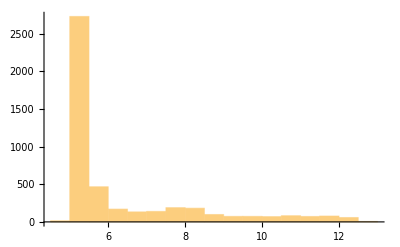

{4.70419,12.5952}

```mathematica
Histogram[Flatten[ImageData[id]]]
minmaxid=MinMax[Flatten[ImageData[id]]]
```

## Calculating results

```mathematica
e=0.01;
lvls=7;
```

#### Over Constrained {1, n} test

```mathematica
mode="OverConstrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id];
```

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

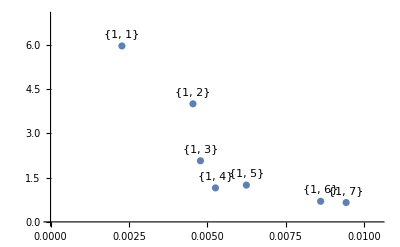

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0,maxX+0.001},{0,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Semi Constrained {1, n} test

```mathematica
mode="SemiConstrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id];
```

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

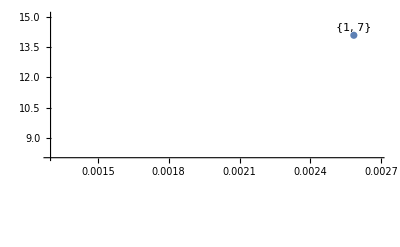

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0.0013,maxX+0.0001},{8,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained {1, n} test

```mathematica
mode="Constrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id];
```

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

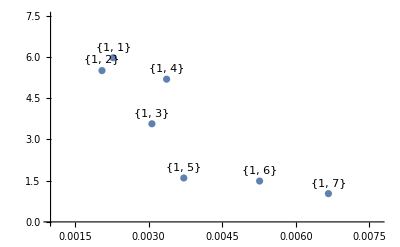

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0.001,maxX+0.001},{0,maxY+1.5}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### All {1, n} test

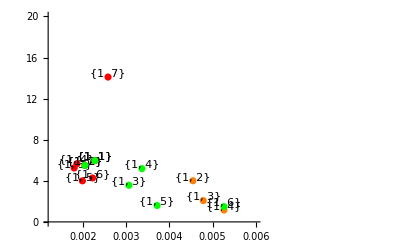

```mathematica
(* Closest Value to {0,0} wins *)
rangexyPlot={{0.0012,0.006},{0,20}};
Show[{
mode="OverConstrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Orange],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
mode="SemiConstrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Red],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
mode="Constrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Green],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
},ImageSize->Scaled[0.5]]
```

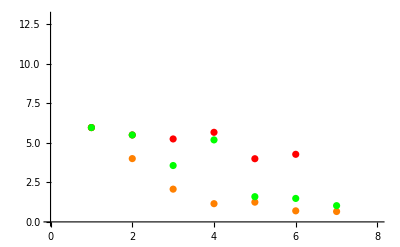

```mathematica
(* Smallest value Wins *)
Show[{
mode="OverConstrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Orange,PlotRange->{{0,lvls+1},{0,13}}],
mode="SemiConstrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Red],
mode="Constrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Green]
},
ImageSize->Scaled[0.5]]
```